# Wolfram Conference Demo

Based on the presentation at https://www.youtube.com/watch?v=JTz4wkD-mxU

### Central Limit Theorem

Note that the Pareto distribution is the most talked about in real life. Not the normal distribution. People are also excited about what is actually realised.

We first define a Pareto random variable.

```mathematica
w:=RandomVariate[ParetoDistribution[1,2]]
```

Here is the help menu for this.

```mathematica
??RandomVariate
```

A Pareto distribution is defined by its minimum value k and shape α.

```mathematica
??ParetoDistribution
```

This code adds up the two random variables.

```mathematica
{w,w}//Total
```

2.44889

The PostFix form allows you to run a function afterwards. Note that this represents the sum of all random variables in a list.

```mathematica
?//
```

Create a list of 1000 Pareto random variables. Take the total. Run the simulation 100 times.

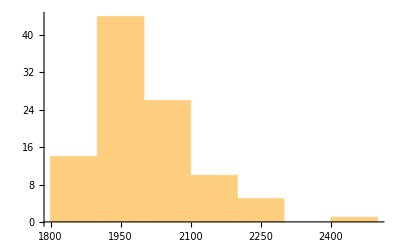

```mathematica
Histogram[Table[Table[w,{1000}]//Total,{100}]]
```

The observation for the Pareto random variable is this. It does not look remotely Gaussian after running the simulation 100 times. The question is: when will the law of large numbers apply? And also, is there a way to verify that it will eventually become a Gaussian using Mathematica as opposed to using an empirical heuristic?

```mathematica
y:=RandomVariate[GammaDistribution[1,1]]
```

We define a random variable that follows the gamma distribution.
Here is the help for this.

```mathematica
??GammaDistribution
```

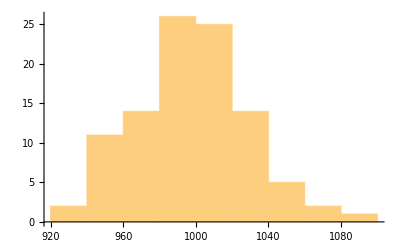

```mathematica
Histogram[Table[Table[y,{1000}]//Total,{100}]]
```

```mathematica
ta=Table[w,{30}];Mean[ta]
```

1.79023

### Law of Large Numbers

```mathematica
r:=RandomVariate[ParetoDistribution[1,1.14]]
```

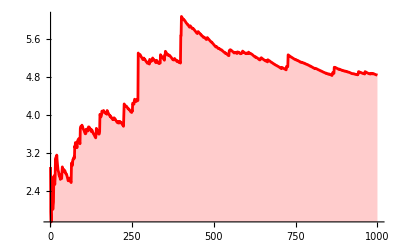

```mathematica
ta=Table[r,{1000}];DiscretePlot[Mean[ta[[1;;i]]],{i,1,Length[ta]},PlotStyle->Red,PlotRange->All]
```

Compare this to a normal distribution.

```mathematica
k:=RandomVariate[NormalDistribution[8,5]]
```

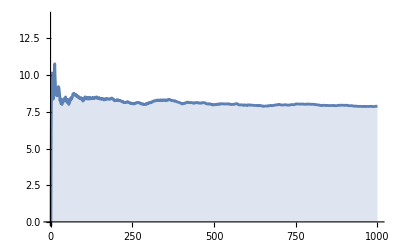

```mathematica
tak=Table[k,{1000}];DiscretePlot[Mean[tak[[1;;i]]],{i,1,Length[tak]},PlotRange->{0,14}]
```

Green lumber fallacy: the best trader in green lumber does not know green is freshly cuy.

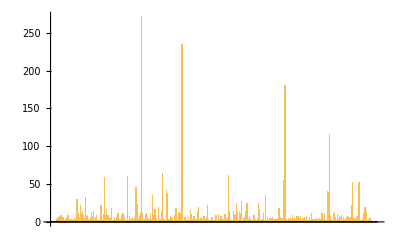

```mathematica
BarChart[ta]
```

Set up an aid to book to do analytical work on the side.

[Image]

```mathematica
Integrate[x^2,{x,0,x}]
```

x^3/3

### covfefe Markov Chain

```mathematica
states={"Fail","C","CO","COV","COVF","COVFE","COVFEF","COVFEFE"}
```

{Fail,C,CO,COV,COVF,COVFE,COVFEF,COVFEFE}

One for starting state to fail straight away. One for each state except for failure. One for identity on "covfefe".

```mathematica
M={{25/26,1/26,0,0,0,0,0,0},{24/26,1/26,1/26,0,0,0,0,0},{24/26,1/26,0,1/26,0,0,0,0},{24/26,1/26,0,0,1/26,0,0,0},{24/26,1/26,0,0,0,1/26,0,0},{24/26,1/26,0,0,0,0,1/26,0},{24/26,1/26,0,0,0,0,0,1/26},{0,0,0,0,0,0,0,1}};
```

```mathematica
TableForm[M,TableHeadings->{states,states}]
```

| Fail | C | CO | COV | COVF | COVFE | COVFEF | COVFEFE
Fail | 25/26 | 1/26 | 0 | 0 | 0 | 0 | 0 | 0
C | 12/13 | 1/26 | 1/26 | 0 | 0 | 0 | 0 | 0
CO | 12/13 | 1/26 | 0 | 1/26 | 0 | 0 | 0 | 0
COV | 12/13 | 1/26 | 0 | 0 | 1/26 | 0 | 0 | 0
COVF | 12/13 | 1/26 | 0 | 0 | 0 | 1/26 | 0 | 0
COVFE | 12/13 | 1/26 | 0 | 0 | 0 | 0 | 1/26 | 0
COVFEF | 12/13 | 1/26 | 0 | 0 | 0 | 0 | 0 | 1/26
COVFEFE | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
procCOVFEFE=DiscreteMarkovProcess[1,M]
```

DiscreteMarkovProcess[1,{{25/26,1/26,0,0,0,0,0,0},{12/13,1/26,1/26,0,0,0,0,0},{12/13,1/26,0,1/26,0,0,0,0},{12/13,1/26,0,0,1/26,0,0,0},{12/13,1/26,0,0,0,1/26,0,0},{12/13,1/26,0,0,0,0,1/26,0},{12/13,1/26,0,0,0,0,0,1/26},{0,0,0,0,0,0,0,1}}]

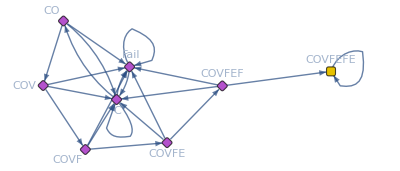

```mathematica
Graph[procCOVFEFE,VertexLabels->Table[i->states[[i]],{i,1,8}]]
```

```mathematica
Export["graph.jpg",%]
```

graph.jpg

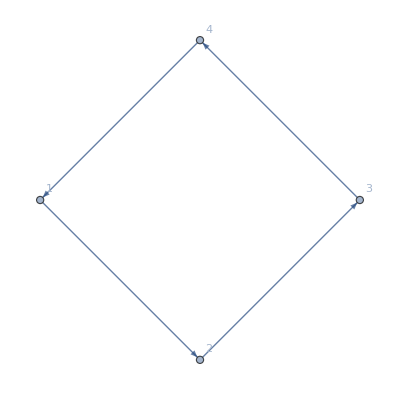

```mathematica
Graph[{1->2,2->3,3->4,4->1},VertexLabels->All]
```

```mathematica
FirstPassageTimeDistribution[procCOVFEFE,8]//Mean
```

8031810176

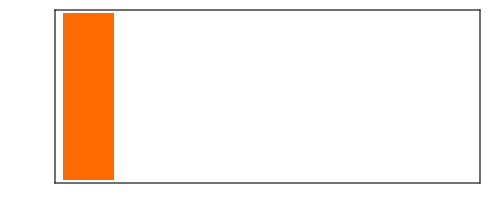
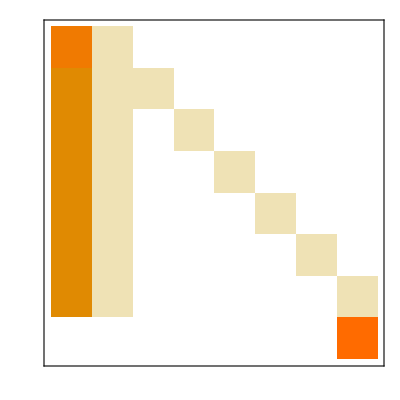
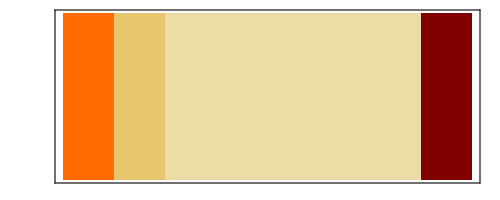
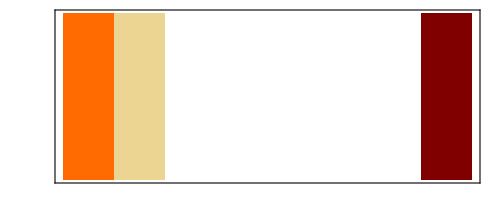
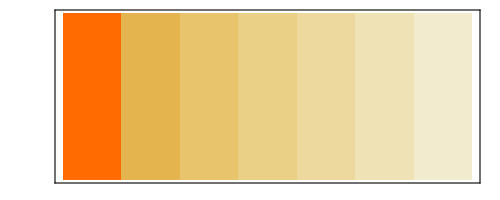
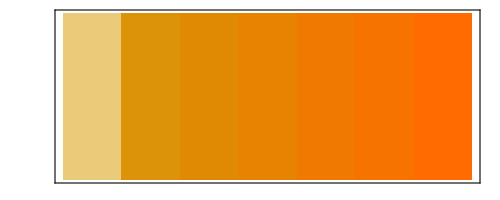
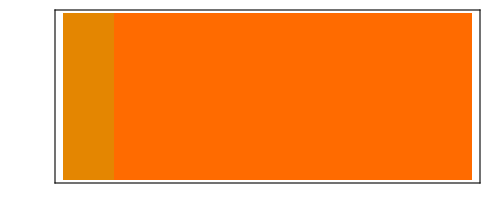
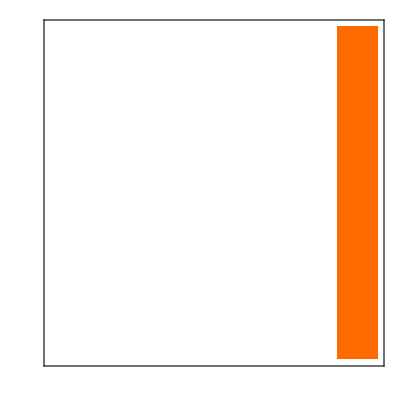
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {8}, {1,…,7}
RecurrentClasses | {8}
TransientClasses | {1,…,7}
AbsorbingClasses | {8}
PeriodicClasses | None
Periods | {}
Irreducible | False
Aperiodic | True
Primitive | False
Transient Properties | 
TransientVisitMean | -Graphics-
TransientVisitVariance | -Graphics-
TransientTotalVisitMean | 7
Limiting Properties | 
ReachabilityProbability | -Graphics-
LimitTransitionMatrix | -Graphics-
Reversible | False

{1.,1.,0.0224305,0.0111299+0.0194242 ⅈ,0.0111299-0.0194242 ⅈ,-0.0112132+0.0192801 ⅈ,-0.0112132-0.0192801 ⅈ,-0.022264}

```mathematica
MarkovProcessProperties[procCOVFEFE]
Eigenvalues[M]//N
```

### AiryAI Simplification

Mathematica enables you to basically copy Ramanujan and explore mathematics. Always use fractions on Mathematica to automatically find closed forms.

```mathematica
PDF[StableDistribution[3/2,1,0,1],x]
```

-(2^(1/3) ⅇ^(x^3/27) (3^(1/3) x AiryAi[x^2/(3 2^(2/3) 3^(1/3))]+3 2^(1/3) AiryAiPrime[x^2/(3 2^(2/3) 3^(1/3))]))/(3 3^(2/3))

Wolfram Engine does not work so well with Manipulate.

```mathematica
Tuples[{a,b,c},3]
```

{{a,a,a},{a,a,b},{a,a,c},{a,b,a},{a,b,b},{a,b,c},{a,c,a},{a,c,b},{a,c,c},{b,a,a},{b,a,b},{b,a,c},{b,b,a},{b,b,b},{b,b,c},{b,c,a},{b,c,b},{b,c,c},{c,a,a},{c,a,b},{c,a,c},{c,b,a},{c,b,b},{c,b,c},{c,c,a},{c,c,b},{c,c,c}}

```mathematica
WolframLanguageData["Integrate","RelationshipCommunityGraph"]
```

-Graphics-

```mathematica
CayleyGraph[AbelianGroup[{2,2,2,2}]]//UndirectedGraph
```